-Graphics3D-

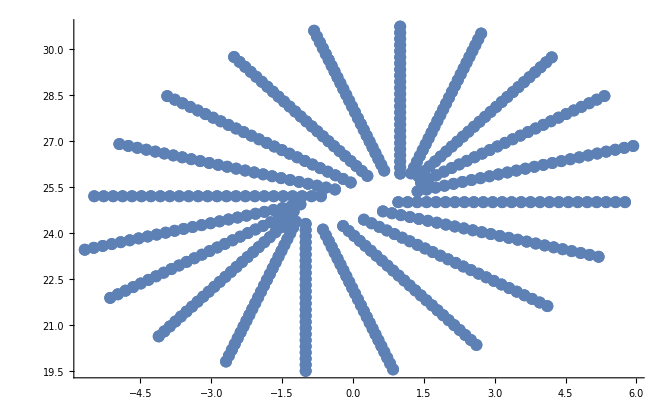

```mathematica
g= {0,0,-1.6};
Subscript[X, i] = {0,0,2};
Subscript[V, bay]=6.1;
r = 0.04;
RPM = 300;
Subscript[V, li]=RPM/60 r 2π;
LaunchAngle = π/4;
dtEject = 0.01;

Subscript[V, ri] = {{0,1,0},{-1,0,0},{0,-1,0},{1,0,0}};
Subscript[X, ri] = {{1,0,0},{0,1,0},{-1,0,0},{0,-1,0}};

Subscript[VV, ri][t_]:={Subscript[V, ri][[1]].RotationMatrix[dTheta[t],{0,0,1}],Subscript[V, ri][[2]].RotationMatrix[dTheta[t],{0,0,1}],Subscript[V, ri][[3]].RotationMatrix[dTheta[t],{0,0,1}],Subscript[V, ri][[4]].RotationMatrix[dTheta[t],{0,0,1}]}

Subscript[XX, ri][t_]:={Subscript[X, ri][[1]].RotationMatrix[dTheta[t],{0,0,1}],Subscript[X, ri][[2]].RotationMatrix[dTheta[t],{0,0,1}],Subscript[X, ri][[3]].RotationMatrix[dTheta[t],{0,0,1}],Subscript[X, ri][[4]].RotationMatrix[dTheta[t],{0,0,1}]}

Trajectory[ X_,V_,G_,T_]:=X+V T + 1/2 G T^2;

dTheta[t_] := (RPM/60)*t*2π;

Main[t_] := Trajectory[Subscript[X, i],Subscript[V, bay]*({0,0,1}.RotationMatrix[LaunchAngle,{1,0,0}]),g,t];

Luna[t_,row_]:=Subscript[XX, ri][t][[row]].RotationMatrix[LaunchAngle,{1,0,0}] + Main[t];

Ejected[T_,row_,t_]:=Trajectory[Luna[T,row],Subscript[VV, ri][T][[row]]+Main'[T],g,t];

Subscript[T, final][T_,row_]:=Solve[Ejected[T,row,t][[3]]==0,t][[2]]

timeBetween = 0.04;

ts[i_,j_]  := {Ejected[i,j,t][[1]],Ejected[i,j,t][[2]]}/.Subscript[T, final][i,j]

Show[
Table[ParametricPlot3D[Luna[t,n],{t,0,2},PlotStyle->{Gray}],{n,1,4}],
Table[ParametricPlot3D[Ejected[0,n,x],{x,0,t/.Subscript[T, final][0,n]}],{n,1,4}],
PlotRange->All
]

Show[
Table[ListPlot[{ts[n*timeBetween,1]}],{n,1,125}],
Table[ListPlot[{ts[n*timeBetween,2]}],{n,1,125}],
Table[ListPlot[{ts[n*timeBetween,3]}],{n,1,125}],
Table[ListPlot[{ts[n*timeBetween,4]}],{n,1,125}],
PlotRange->All
]
```